# Vaje iz Mathematice, 2. del

### 1. naloga:

Izračunaj vrednost izraza  30! -20! +110

```mathematica
izr=30!-20!+110
```

265252859812188625734300303360110

Kakšna je 10. števka od leve proti desni?

```mathematica
IntegerDigits[izr][[10]]
```

8

Rezultat razcepi na prafaktorje.

```mathematica
pra=FactorInteger[izr]
```

{{2,1},{5,1},{11,3},{41,1},{101,1},{897840721,1},{5360156751159421,1}}

Katero je največje praštevilo v razcepu?

```mathematica
Last[pra][[1]]
```

5360156751159421

Katero praštevilo nastopa v razcepu z najvišjo potenco?

```mathematica
sort[pra]
```

sort[{{2,1},{5,1},{11,3},{41,1},{101,1},{897840721,1},{5360156751159421,1}}]

```mathematica
Reverse[{1,2,3}]
```

{3,2,1}

```mathematica
Last[Last[Sort[Map[Reverse,pra]]]]
```

11

### 2. naloga:

Poišči vse delitelje števila 16524000.

```mathematica
n=16524000;
```

```mathematica
delitelji=Divisors[n];
```

Katera od njih so praštevila?

```mathematica
Select[delitelji,PrimeQ]
```

{2,3,5,17}

S kakšnimi potencami nastopajo v razcepu števila 16524000?

```mathematica
FactorInteger[n]
```

{{2,5},{3,5},{5,3},{17,1}}

### 3. naloga:

Izračunaj  lim_(x→2) (x^3-4 x^2+2x+4)/(x^5-9x-14)

Izračunaj  lim_(x→0) (arctg (7x))/(arcsin (8x))

Izračunaj  lim_(x→5) (x^2-25)ctg (π x)

Izračunaj  lim_(x→π) (1+cos x)/(2 √(π x)-π-x)

```mathematica
Limit[(1+Cos[x])/(2*Sqrt[Pi*x] - Pi - x) , x -> Pi]
```

-2 π

Izračunaj levo limito:  lim_(x→0^-) |x|ctg x

```mathematica
Limit[Abs[x]*Cot[x], x -> 0, Direction->"FromBelow"]
```

-1

Izračunaj desno limito:  lim_(x→0^+) |x|ctg x

```mathematica
Limit[Abs[x]*Cot[x], x -> 0, Direction->"FromAbove"]
```

1

### 4. naloga:

Izračunaj prvi odvod funkcije  y=2sin (2x+1)  cos (x)

```mathematica
D[2*Sin[2*x+1]*Cos[x],x]
```

4 Cos[x] Cos[1+2 x]-2 Sin[x] Sin[1+2 x]

```mathematica
f[x_]:= 2*Sin[2*x+1]*Cos[x];
```

```mathematica
f'[x]
```

4 Cos[x] Cos[1+2 x]-2 Sin[x] Sin[1+2 x]

```mathematica
f''[x]
```

-8 Cos[1+2 x] Sin[x]-10 Cos[x] Sin[1+2 x]

Izračunaj prvi odvod funkcije  y=x ln (2x)

Izračunaj prvi odvod funkcije  y=(3x-2)^(1/3)/(√(2x+1))

Izračunaj drugi odvod funkcije  y=(x+1)^x

### 5. naloga:

Numerično izračunaj ničle polinoma  x^7-2 x^6-x^5-2 x^4+12 x^2-x+1.

```mathematica
nicle=NSolve [x^7 - 2x^6 - x^5 - 2x^4 + 12x^2 - x + 1==0,x]
```

{{x→-1.37527},{x→-0.356206-1.47367 ⅈ},{x→-0.356206+1.47367 ⅈ},{x→0.040941-0.283889 ⅈ},{x→0.040941+0.283889 ⅈ},{x→1.59494},{x→2.41086}}

```mathematica
nicle=x/.NSolve [x^7 - 2x^6 - x^5 - 2x^4 + 12x^2 - x + 1==0,x]
```

{-1.37527,-0.356206-1.47367 ⅈ,-0.356206+1.47367 ⅈ,0.040941-0.283889 ⅈ,0.040941+0.283889 ⅈ,1.59494,2.41086}

Katere od teh ničel so realne?

```mathematica
RealQ[x_] := Element[x,Reals]
Select[nicle,RealQ]
```

{-1.37527,1.59494,2.41086}

Kakšna je največja absolutna vrednost ničle?

```mathematica
Max[Abs[nicle]]
```

2.41086

```mathematica
Max[Map[Abs,nicle]]
```

2.41086

### 6. naloga:

Razcepi polinom  x^7+2 x^6-80 x^5+232 x^4+175 x^3-826 x^2+256x-1056  na linearne in kvadratne faktorje.

```mathematica
pa=[x^7+2 x^6-80 x^5+232 x^4+175 x^3-826 x^2+256x-1056]
Factor[pa]
```

```mathematica
Pa=x^7+2 x^6-80 x^5+232 x^4+175 x^3-826 x^2+256x-1056
```

-1056+256 x-826 x^2+175 x^3+232 x^4-80 x^5+2 x^6+x^7

```mathematica
Factor[Pa]
```

(-4+x)^2 (-3+x) (2+x) (11+x) (1+x^2)

Razcepi isti polinom na linearne faktorje.

```mathematica
Factor[Pa, Extension->I]
```

(-4+x)^2 (-3+x) (-ⅈ+x) (ⅈ+x) (2+x) (11+x)

Faktoriziraj trigonometrični izraz  sin (x)+cos (2x)

```mathematica
Factor[Sin[x] + Cos[2x], Trig -> True]
```

(Cos[x/2]-Sin[x/2])^2 (1+2 Sin[x])

### 7. naloga:

Definiraj polinom  (x^2 (y-1)-x^3 y^5+(x-1)^7 x y (x^2+2x y+y^3))^2  kot novo spremenljivko.

```mathematica
p= (x^2 (y-1)-x^3 y^5+(x-1)^7 x y (x^2+2x y+y^3))^2
```

(x^2 (-1+y)-x^3 y^5+(-1+x)^7 x y (x^2+2 x y+y^3))^2

Razširi polinom tako, da dobiš vsoto monomov.

```mathematica
Expand[p]
```

x^4-2 x^4 y+2 x^5 y-14 x^6 y+42 x^7 y-70 x^8 y+70 x^9 y-42 x^10 y+14 x^11 y-2 x^12 y+5 x^4 y^2-30 x^5 y^2+99 x^6 y^2-196 x^7 y^2+301 x^8 y^2-518 x^9 y^2+1071 x^10 y^2-2020 x^11 y^2+3005 x^12 y^2-3432 x^13 y^2+3003 x^14 y^2-2002 x^15 y^2+1001 x^16 y^2-364 x^17 y^2+91 x^18 y^2-14 x^19 y^2+x^20 y^2-4 x^4 y^3+32 x^5 y^3-140 x^6 y^3+504 x^7 y^3-1596 x^8 y^3+4088 x^9 y^3-8036 x^10 y^3+12016 x^11 y^3-13728 x^12 y^3+12012 x^13 y^3-8008 x^14 y^3+4004 x^15 y^3-1456 x^16 y^3+364 x^17 y^3-56 x^18 y^3+4 x^19 y^3+2 x^3 y^4-10 x^4 y^4-14 x^5 y^4+294 x^6 y^4-1386 x^7 y^4+3962 x^8 y^4-7994 x^9 y^4+12010 x^10 y^4-13728 x^11 y^4+12012 x^12 y^4-8008 x^13 y^4+4004 x^14 y^4-1456 x^15 y^4+364 x^16 y^4-56 x^17 y^4+4 x^18 y^4-2 x^3 y^5+16 x^4 y^5-68 x^5 y^5+252 x^6 y^5-798 x^7 y^5+2044 x^8 y^5-4018 x^9 y^5+6008 x^10 y^5-6864 x^11 y^5+6006 x^12 y^5-4004 x^13 y^5+2002 x^14 y^5-728 x^15 y^5+182 x^16 y^5-28 x^17 y^5+2 x^18 y^5+4 x^3 y^6-56 x^4 y^6+362 x^5 y^6-1454 x^6 y^6+3990 x^7 y^6-7966 x^8 y^6+11942 x^9 y^6-13658 x^10 y^6+11970 x^11 y^6-7994 x^12 y^6+4002 x^13 y^6-1456 x^14 y^6+364 x^15 y^6-56 x^16 y^6+4 x^17 y^6+4 x^5 y^7-28 x^6 y^7+84 x^7 y^7-140 x^8 y^7+140 x^9 y^7-84 x^10 y^7+28 x^11 y^7-4 x^12 y^7+x^2 y^8-14 x^3 y^8+91 x^4 y^8-364 x^5 y^8+1001 x^6 y^8-2002 x^7 y^8+3003 x^8 y^8-3432 x^9 y^8+3003 x^10 y^8-2002 x^11 y^8+1001 x^12 y^8-364 x^13 y^8+91 x^14 y^8-14 x^15 y^8+x^16 y^8+2 x^4 y^9-14 x^5 y^9+42 x^6 y^9-70 x^7 y^9+70 x^8 y^9-42 x^9 y^9+14 x^10 y^9-2 x^11 y^9+x^6 y^10

Razvij polinom po potencah x  (koeficienti bodo polinomi v y).

```mathematica
Collect[p,x]
```

x^20 y^2+x^2 y^8+x^19 (-14 y^2+4 y^3)+x^18 (91 y^2-56 y^3+4 y^4+2 y^5)+x^17 (-364 y^2+364 y^3-56 y^4-28 y^5+4 y^6)+x^13 (-3432 y^2+12012 y^3-8008 y^4-4004 y^5+4002 y^6-364 y^8)+x^3 (-2 (-1+y) y^4+4 y^6-14 y^8)+x^15 (-2002 y^2+4004 y^3-1456 y^4-728 y^5+364 y^6-14 y^8)+x^16 (1001 y^2-1456 y^3+364 y^4+182 y^5-56 y^6+y^8)+x^14 (3003 y^2-8008 y^3+4004 y^4+2002 y^5-1456 y^6+91 y^8)+x^12 (2 (-1+y) y+3003 y^2-13728 y^3+12012 y^4+6006 y^5-7994 y^6-4 y^7+1001 y^8)+x^7 (-42 (-1+y) y-14 y^2+140 (-1+y) y^2+364 y^3-1456 y^4-70 (-1+y) y^4-728 y^5+3990 y^6+84 y^7-2002 y^8-70 y^9)+x^9 (-70 (-1+y) y-364 y^2+84 (-1+y) y^2+4004 y^3-8008 y^4-14 (-1+y) y^4-4004 y^5+11942 y^6+140 y^7-3432 y^8-42 y^9)+x^5 (-2 (-1+y) y+28 (-1+y) y^2+4 y^3-56 y^4-42 (-1+y) y^4-28 y^5-2 (-1+y) y^5+364 y^6+4 y^7-364 y^8-14 y^9)+x^11 (-14 (-1+y) y-2002 y^2+4 (-1+y) y^2+12012 y^3-13728 y^4-6864 y^5+11970 y^6+28 y^7-2002 y^8-2 y^9)+x^4 ((-1+y)^2-4 (-1+y) y^2+4 y^4+14 (-1+y) y^4+2 y^5-56 y^6+91 y^8+2 y^9)+x^10 (42 (-1+y) y+1001 y^2-28 (-1+y) y^2-8008 y^3+12012 y^4+2 (-1+y) y^4+6006 y^5-13658 y^6-84 y^7+3003 y^8+14 y^9)+x^8 (70 (-1+y) y+91 y^2-140 (-1+y) y^2-1456 y^3+4004 y^4+42 (-1+y) y^4+2002 y^5-7966 y^6-140 y^7+3003 y^8+70 y^9)+x^6 (14 (-1+y) y+y^2-84 (-1+y) y^2-56 y^3+364 y^4+70 (-1+y) y^4+182 y^5-1454 y^6-28 y^7+1001 y^8+42 y^9+y^10)

Kakšna je najvišja potenca posameznih spremenljivk, ki se pojavita v polinomu?

```mathematica
Exponent[p,{x,y}]
```

{20,10}

### 8.naloga:

Določi vsa realna števila, ki zadoščajo neenačbi  (|x-3|)/(x+1)>√(3-2x)

```mathematica
Reduce[Abs[x-3]/ (x+1)> Sqrt[3-2x]]
```

-1<x<1||1<x≤3/2

### 9. naloga:

Definiraj  (x^2-1)/(x^2-4)  kot funkcijo f spremenljivke x in nariši njen graf na intervalu [-5,5].

```mathematica
Clear[f]
```

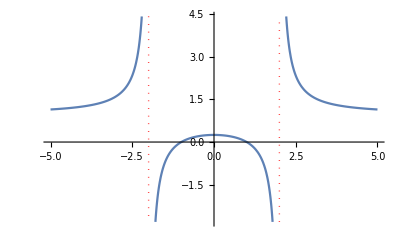

```mathematica
f[x_] := (x^2-1)/(x^2-4)
Plot[f[x], {x, -5,5},ExclusionsStyle -> {{Red,Dotted}}]
```

Določi ničle.

```mathematica
nicle=x/. Solve[f[x]==0,x]
```

{-1,1}

Določi pole in razišči obnašanje funkcije v okolici polov.

```mathematica
poli = x/.Solve[Denominator[f[x]]==0,x]
Limit[f[x], x -> poli, Direction->"FromAbove"]
Limit[f[x], x -> poli, Direction->"FromBelow"]
```

{-2,2}

{-∞,∞}

{∞,-∞}

Izračunaj limiti v neskončnosti.

```mathematica
Limit[f[x], x -> {-Infinity,Infinity}]
```

{1,1}

Določi stacionarne točke.

```mathematica
stac = x/.Solve[D[f[x],x] == 0 ]
```

{0}

Določi vrsto stacionarnih točk (lokalni minimum, lokalni maksimum, prevoj).

```mathematica
D[f[x], {x,2}] /. x -> stac
```

{-3/8}

Določi intervale konveksnosti.

```mathematica
Reduce[D[f[x],{x,2}] >0]
```

x<-2||x>2

Določi intervale konkavnosti.

```mathematica
Reduce[D[f[x],{x,2}] <0]
```

-2<x<2

### 10. naloga:

Analiziraj funkcijo y=arctg x^2/(x^2-1). Zgleduj se po prejšnji nalogi.

### 11. naloga:

Določi tangento na funkcijo h(x)=sin^2 x-cos x  v točki x=2. Rezultat predstavi s sliko.

### 12. naloga:

Dana sta vektorja  (v⃗)_1=(1,2,3)  in  (v⃗)_2=(-3,-2,5). Zapiši ju kot dve spremenljivki.

Izračunaj njun skalarni produkt.

Izračunaj njun vektorski produkt.

Kateri od vektorjev je daljši?

Sestavi enačbo ravnine, ki gre skozi točko (1,1,1) in ima normalo v smeri vektorskega produkta.

### 13. naloga:

Dana je matrika  M=(9 | 2 | -3
3 | 2 | 1
6 | 4 | -1).  Zapiši jo kot spremenljivko.

Izračunaj njeno determinanto.

Izračunaj njene lastne vrednosti.

Izračunaj njene lastne vektorje.

Ali je matrika diagonalizabilna?

Matriko želimo diagonalizirati. Konstruiraj diagonalno matriko (po diagonali ima lastne vrednosti), prehodno matriko (za stolpce ima lastne vektorje) in inverz prehodne matrike.

Preveri, ali velja pogoj za diagonalizabilnost.

### 14. naloga:

Dana je parametrično podana krivulja  (((3-t) sin t)/(t+1),cos (t) sin (2t)). Definiraj jo kot funkcijo ene spremenljivke.

Nariši krivuljo za  t∈[0,5].

Krivulja seče samo sebe natanko dvakrat. S pomočjo numeričnega reševanja enačb (FindRoot) poišči približek presečišč. Enačbo nastavi tako da izenačiš krivuljo, parametrizirano s parametrom t, s krivuljo, parametrizirano s parametrom s. Potem s spreminjanjem začetnih približkov parametrov t in s poskusi določiti vrednosti parametrov, pri katerih pride do samopresečič.

Iz dobljenih rešitev sestavi točki.

Grafično preveri, ali gre za pravilen izračun.

### 15. naloga:

Naj bodo a⃗, b⃗ in c⃗ vektorji v R^3.
S simboličnim računom dokaži identiteto  a⃗×(b⃗×c⃗)=(a⃗·c⃗)b⃗-(a⃗·b⃗)c⃗

### 16. naloga:

Dokaži, da za poljubni 2×2 matriki A in B velja enakost  (A B)^-1=B^-1 A^-1.